```mathematica
values={1,2,3,4,5,6};
weights={1/3,1/6,1/6,1/9,1/9,1/9};
expValue=values.weights;
MaxEntP[x_,b_]:=Table[Exp[-b*x[[i]]],{i,1,Length[x]}]/Sum[Exp[-b*x[[j]]],{j,1,Length[x]}];
lagmult=NSolve[values.MaxEntP[values,b]==expValue,b,Reals]
MaxEntP[values,b]/.lagmult[[1]]
```

{{b→0.236341}}

{0.277758,0.219293,0.173134,0.136692,0.10792,0.0852037}

```mathematica
expValue2=(values^2).weights;
lagmults=NSolve[(values^2).MaxEntP[values^2,b]==expValue2,b,Reals]
MaxEntP[values,b]/.lagmults[[1]]
```

{{b→0.0311551}}

{0.179912,0.174393,0.169044,0.163858,0.158832,0.15396}

```mathematica
MaxEntP2[f_,g_,a_,b_]:=Table[Exp[-a*f[[i]]-b*g[[i]]],{i,1,Length[f]}]/Sum[Exp[-a*f[[i]]-b*g[[i]]],{i,1,Length[f]}];
MaxEntP2[values,values^2,a,b];
lagmults2=NSolve[values.MaxEntP2[values,values^2,a,b]==expValue&&(values^2).MaxEntP2[values,values^2,a,b]==expValue2,{a,b},Reals];
```

```mathematica
MaxEntP2[f_,g_,a_,b_]:=Table[Exp[-a*f[[i]]-b*g[[i]]],{i,1,Length[f]}]/Sum[Exp[-a*f[[i]]-b*g[[i]]],{i,1,Length[f]}];
MaxEntP2[values,values^2,a,b];
lagmults2=NSolve[values.MaxEntP2[values,values^2,a,b]==expValue&&(values^2).MaxEntP2[values,values^2,a,b]==expValue2,{a,b},Reals];
```

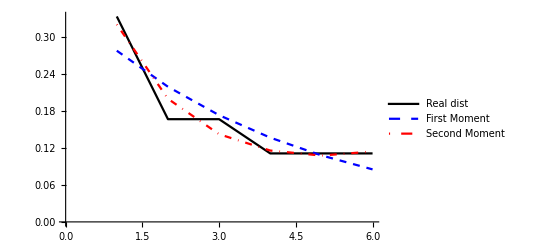

```mathematica
ListLinePlot[{N[weights], MaxEntP[values,b]/.lagmult[[1]], MaxEntP2[values,values^2,a,b]/.lagmults2[[1]]},PlotStyle->{{Black},{Blue,Dashed},{Red,DotDashed}},PlotLegends->{"Real dist","First Moment","Second Moment"}]
```